```mathematica
values = {1,25,25.01,500,5000}
```

{1,25,25.01,500,5000}

```mathematica
s1=Apply[NDSolve[{x'[t]==10 (-x[t]+y[t]),y'[t]==24.5 x[t]-y[t]-x[t] z[t], z'[t] ==-(8 z[t])/3+x[t]y[t], z[0]== x[0]==y[0]==#1},{x,y, z},{t,1000}]&, values]
```

{{x→InterpolatingFunction[{{0., 1000.}}, <>],y→InterpolatingFunction[{{0., 1000.}}, <>],z→InterpolatingFunction[{{0., 1000.}}, <>]}}

```mathematica
s2=Apply[NDSolve[{x'[t]==10 (-x[t]+y[t]),y'[t]==24.5 x[t]-y[t]-x[t] z[t], z'[t] ==-(8 z[t])/3+x[t]y[t], z[0]== x[0]==y[0]==#2},{x,y, z},{t,1000}]&, values]
```

{{x→InterpolatingFunction[{{0., 1000.}}, <>],y→InterpolatingFunction[{{0., 1000.}}, <>],z→InterpolatingFunction[{{0., 1000.}}, <>]}}

```mathematica
s3=Apply[NDSolve[{x'[t]==10 (-x[t]+y[t]),y'[t]==24.5 x[t]-y[t]-x[t] z[t], z'[t] ==-(8 z[t])/3+x[t]y[t], z[0]== x[0]==y[0]==#3},{x,y, z},{t,1000}]&, values]
```

{{x→InterpolatingFunction[{{0., 1000.}}, <>],y→InterpolatingFunction[{{0., 1000.}}, <>],z→InterpolatingFunction[{{0., 1000.}}, <>]}}

```mathematica
s4=Apply[NDSolve[{x'[t]==10 (-x[t]+y[t]),y'[t]==24.5x[t]-y[t]-x[t] z[t], z'[t] ==-(8 z[t])/3+x[t]y[t], z[0]== x[0]==y[0]==#4},{x,y, z},{t,1000}]&, values]
```

{{x→InterpolatingFunction[{{0., 1000.}}, <>],y→InterpolatingFunction[{{0., 1000.}}, <>],z→InterpolatingFunction[{{0., 1000.}}, <>]}}

```mathematica
s5=Apply[NDSolve[{x'[t]==10 (-x[t]+y[t]),y'[t]==24.5 x[t]-y[t]-x[t] z[t], z'[t] ==-(8 z[t])/3+x[t]y[t], z[0]== x[0]==y[0]==#5},{x,y, z},{t,1000}]&, values]
```

{{x→InterpolatingFunction[{{0., 1000.}}, <>],y→InterpolatingFunction[{{0., 1000.}}, <>],z→InterpolatingFunction[{{0., 1000.}}, <>]}}

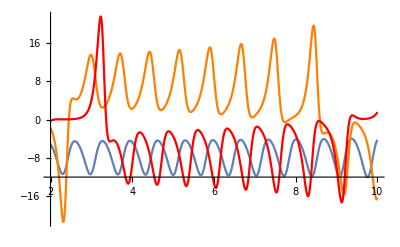

```mathematica
Show[
Plot[Evaluate[y[t]/.s1],{t,2,10},PlotRange->All],
Plot[Evaluate[y[t]/.s4],{t,2,10},PlotRange->All, PlotStyle->{Orange}],
Plot[Evaluate[y[t]/.s5],{t,2,10},PlotRange->All, PlotStyle->{Red}]]
```

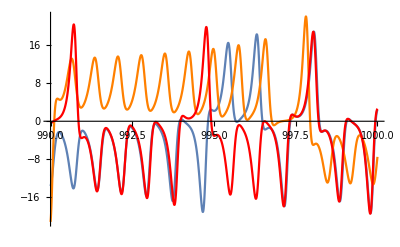

```mathematica
Show[
Plot[Evaluate[y[t]/.s1],{t,990,1000},PlotRange->All],
Plot[Evaluate[y[t]/.s4],{t,990,1000},PlotRange->All, PlotStyle->{Orange}],
Plot[Evaluate[y[t]/.s5],{t,990,1000},PlotRange->All,PlotStyle->{Red}]]
```

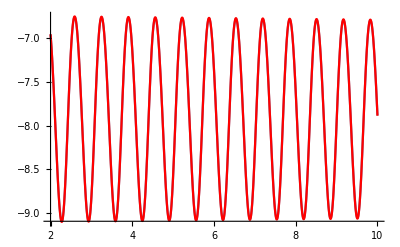

```mathematica
Show[
Plot[Evaluate[y[t]/.s2],{t,2,10},PlotRange->All],
Plot[Evaluate[y[t]/.s3],{t,2,10},PlotRange->All,PlotStyle->{Red}]]
```

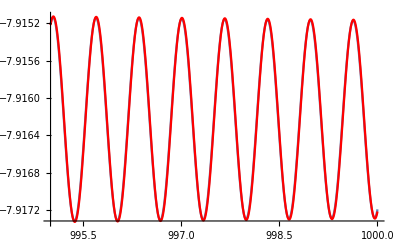

```mathematica
Show[
Plot[Evaluate[y[t]/.s2],{t,995,1000},PlotRange->All],
Plot[Evaluate[y[t]/.s3],{t,995,1000},PlotRange->All,PlotStyle->{Red}]]
```

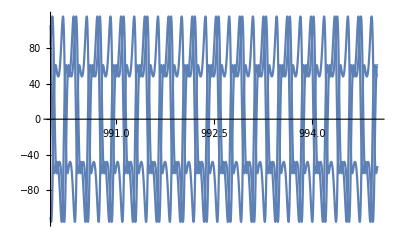

```mathematica
Show[
Plot[Evaluate[y[t]/.s1],{t,990,995},PlotRange->All],
Plot[Evaluate[y[t]/.s4],{t,990,995},PlotRange->All],
Plot[Evaluate[y[t]/.s5],{t,990,995},PlotRange->All]]
```

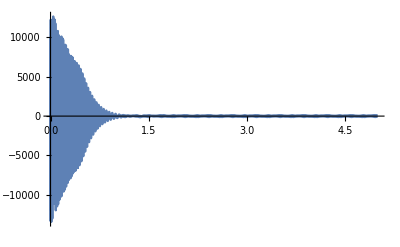

NDSolve::underdet: There are more dependent variables, {x[t],y[t],z[t]}, than equations, so the system is underdetermined.

```mathematica
Show[
Plot[Evaluate[y[t]/.s1],{t,0,5},PlotRange->All],
Plot[Evaluate[y[t]/.s4],{t,0,5},PlotRange->All],
Plot[Evaluate[y[t]/.s5],{t,0,5},PlotRange->All]]
```

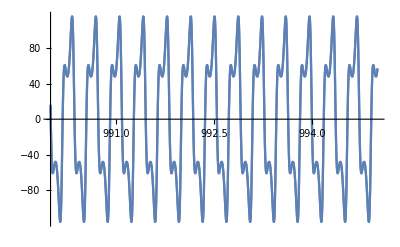

```mathematica
Show[
Plot[Evaluate[y[t]/.s2],{t,990,995},PlotRange->All],
Plot[Evaluate[y[t]/.s3],{t,990,995},PlotRange->All]]
```

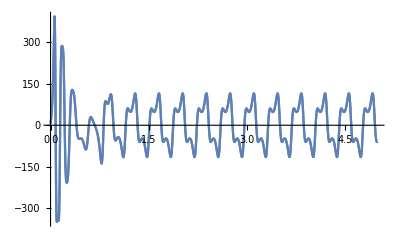

```mathematica
Show[
Plot[Evaluate[y[t]/.s2],{t,0,5},PlotRange->All],
Plot[Evaluate[y[t]/.s3],{t,0,5},PlotRange->All]]
```

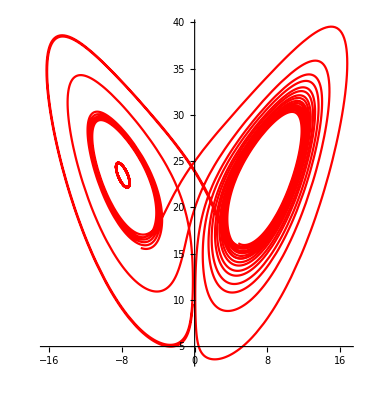

```mathematica
Show[
ParametricPlot[
Evaluate[
{x[t], z[t]} /.Part[s1]
],
{t,25, 35},
PlotRange->All, PlotStyle->{Red}
],ParametricPlot[
Evaluate[
{x[t], z[t]} /.Part[s2]
],
{t,25, 35},
PlotRange->All, PlotStyle->{Red}
], ParametricPlot[
Evaluate[
{x[t], z[t]} /.Part[s3]
],
{t,25, 35},
PlotRange->All, PlotStyle->{Red}
], ParametricPlot[
Evaluate[
{x[t], z[t]} /.Part[s4]
],
{t,25, 35},
PlotRange->All, PlotStyle->{Red}
]]
```